```mathematica
(* Valor de J*)
J=100;
```

```mathematica
(*Elementos de Matriz*)
(*Sz[m_]=m;*)
SM2[m_]=Sqrt[J(J+1)-m(m+1)]*Sqrt[J(J+1)-(m+1)(m+2)];
Sm2[m_]=Sqrt[J(J+1)-m(m-1)]*Sqrt[J(J+1)-(m-1)(m-2)];
SMSm[m_]=J(J+1)-m(m-1);
SmSM[m_]=J(J+1)-m(m+1);
(* Construyendo Matrices de manera eficiente *)

(*Paridad positiva*)
SzPP=DiagonalMatrix[Table[Sz[-J+2(k-1)],{k,1,J+1}]];
SGPP=DiagonalMatrix[Table[(SMSm[-J+2(k-1)]+SmSM[-J+2(k-1)]),{k,1,J+1}]];
SP2PP=SparseArray[Table[{k+1,k}->SM2[-J+2(k-1)],{k,1,J}],{J+1,J+1}];

(*Paridad negativa*)
SzPN=DiagonalMatrix[Table[Sz[-J+1+2(k-1)],{k,1,J}]];
SGPN=DiagonalMatrix[Table[(SMSm[-J+1+2(k-1)]+SmSM[-J+1+2(k-1)]),{k,1,J}]];
SP2PN=SparseArray[Table[{k+1,k}->SM2[-J+1+2(k-1)],{k,1,J-1}],{J,J}];
SLPN=SP2PN+Transpose[SP2PN];
```

```mathematica
(* Construyendo Matrices de manera eficiente *)
(*Sin Paridad*)
Sz=DiagonalMatrix[Table[-J+k-1,{k,1,2J+1}]];
SG=DiagonalMatrix[Table[(SMSm[-J+k-1]+SmSM[-J+k-1]),{k,1,2J+1}]];
SP2=SparseArray[Table[{k+2,k}->SM2[-J+k-1],{k,1,2J-1}],{2J+1,2J+1}];
SL=SP2+Transpose[SP2];
Sxp = SparseArray[Table[{k+1,k}->√SmSM[-J+k-1],{k,1,2J}],{2J+1,2J+1}];
Sx=(Sxp+Transpose[Sxp])/2;
Qp = SparseArray[Table[{k+1,k}->(√SmSM[-J+k-1])/(√2 √(2J+1-k)),{k,1,2J}],{2J+1,2J+1}];
QQ=Qp+Transpose[Qp];
QQ2 = QQ.QQ;
PP=-ⅈ(Qp-Transpose[Qp]);
PP2 =PP.PP;
```

```mathematica
SP2PP//MatrixForm
```

```mathematica
IJ= J IdentityMatrix[2J+1];
(*Operadores*)
(*Jz/J+ I*)
Op=(Sz+IJ)/J;
```

```mathematica
ϵ=1;
γy=0;
γx=-2.0; (*γx=2α*)
λ=ϵ(γx-γy)/(2(2J-1));
γ=ϵ (γx+γy)/(2(2J-1));
(*Hamiltoniano completo*)
H1=ϵ Sz+(λ/2)SL+(γ/2)SG;
(* eigenvalores *)
{enNO,evNO}=Eigensystem[H1];(*Eigenvalues[N[H1,20]];*)
en=Sort[enNO];
ev=evNO[[Ordering[enNO]]];
```

```mathematica
(*ev=evNO[[Ordering[enNO]]];
co=Transpose[ev][[1]]; (*Componentes del estado !J -J> en la base de vectores propios de H*)*)
(*OpE=Conjugate[ev].Op.Transpose[ev];  (*Matriz Op en la base de energías*)
(*OpED=Conjugate[ev].OpD.Transpose[ev];  (*Matriz OpD en la base de energías*)*)
DSco=Compile[{{t, _Real}},Re[Conjugate[co Exp[-I en t]].OpE.(co Exp[-I en t])]];*)(*Función para calcular <ψ t| Op | ψ t>*)
(*DSDco=Compile[{{t, _Real}},Re[Conjugate[co Exp[-I en t]].OpED.(co Exp[-I en t])]]; (*Función para calcular <ψ t| OpD | ψ t>*)*)
```

```mathematica
(*Funciones de ayuda. (Ayudan a minimizar llamadas repetidas)*)
Conmutador[A_,B_]:=A.B-B.A 
MatrixSquared[A_]:=ConjugateTranspose[A] .A
BasisChange[A_,U_]:=ConjugateTranspose[U] .A.U
(*Matrices en la base de energías*)
QQE=ev.QQ.Transpose[ev];
QQ2E=ev.QQ2.Transpose[ev];
PPE=ev.PP.Transpose[ev];
PP2E=ev.PP2.Transpose[ev];
fase[t_]:=DiagonalMatrix[Exp[-I en t]];
QQET[t_]:=BasisChange[QQE,fase[t]];
QQ2ET[t_]:=BasisChange[QQ2E,fase[t]];
PPET[t_]:=BasisChange[PPE,fase[t]];
PP2ET[t_]:=BasisChange[PP2E,fase[t]];

ConQ[t_]:=Conmutador[QQE,QQET[t]];

ConQ2[t_]:= MatrixSquared[ConQ[t]];
(*Función para calcular el MOTOC de [Q(0),Q(t)]*)
```

```mathematica
(* Estados coherentes*)
(*Funciones de ayuda. (Ayudan a minimizar llamadas repetidas)*)
Conmutador[A_,B_]:=A.B-B.A 
MatrixSquared[A_]:=ConjugateTranspose[A] .A
BasisChange[A_,U_]:=ConjugateTranspose[U] .A.U
JzE=ev.Sz.Transpose[ev];
fase[t_]:=DiagonalMatrix[Exp[-I en t]];
JzET[t_]:=BasisChange[JzE,fase[t]];
ConJz[t_]:=Conmutador[JzE,JzET[t]];
ConJz2[t_]:= MatrixSquared[ConJz[t]];
(*Función para calcular el MOTOC de [Jz(0),Jz(t)]*)
```

```mathematica
LogFact[mm_]:=If[mm==0,0,N[Log[(mm)!]]];
Coeflog[jj_,z1_,nn_]:=1/2 LogFact[2 jj]-jj N[Log[1+Abs[z1]^2]]-1/2 LogFact[nn]-1/2 LogFact[2jj-nn];
zz[Q_,P_]:= (Q - ⅈ P)/√(4 -Q^2-P^2);
Coh[Q_,P_]:= Table[If[zz[Q,P]==0 && n==1,1,Exp[Coeflog[J,zz[Q,P],n-1]] zz[Q,P]^(n-1)],{n,1,2J+1}];
(*Coh[Q_,P_]:=(MatrixExp[zz[Q,P]* SpE].Transpose[ev][[1]] )*(1 -(Q^2+P^2)/4)^J*)
```

```mathematica
(*Transpose[ev][[1]] : Componentes del estado !J -J> en la base de vectores propios de H*)
SpE=ev.Sxp.Transpose[ev];  (* S+ en la base de autoestados*)
```

```mathematica
MOTOC[t_,co_]:=Re[co.ConQ2[t].co] ;
QQ1[t_,co_]:=Re[co.QQET[t].co] ;
QQ1c[t_,co_]:=Re[co.QQ2ET[t].co] ;
FOTOCQ[t_,co_]:=Re[QQ1c[t,co]]-QQ1[t,co]^2 ;
PP1[t_,co_]:=Re[co.PPET[t].co] ;
PP1c[t_,co_]:=Re[co.PP2ET[t].co] ;
FOTOCP[t_,co_]:=Re[PP1c[t,co]]-PP1[t,co]^2 ;
```

```mathematica
(*Funciones para paralelizar y ver el progreso*)
SetAttributes[monitorParallelTable,HoldAll]
monitorParallelTable[expr_,iter__List,updatethreshold_]:=Module[{counter=1,thresh=updatethreshold},SetSharedVariable[counter];
ParallelEvaluate[localcounter=1;];
Monitor[ParallelTable[If[localcounter≥thresh,counter=counter+localcounter;localcounter=1,localcounter++];expr,iter],counter]]
(*Funcion para calcular FOTOC en terminos de Q, P*)
calcFOTOC[Q_,P_,ts_]:=
Module[{co},
co=ev.Coh[Q,P];
monitorParallelTable[(FOTOCQ[tv,co]+FOTOCP[tv,co])/2.,{tv,ts},1]
]
```

```mathematica
ts=Table[t,{t,0,35,0.1}];
Qs={0.,0.1,0.2,0.3};
ftcs=Table[calcFOTOC[Q,0,ts],{Q,Qs}];
```

```mathematica
(*Exportar FOTOCS*)
Export["LMG_FOTOC.csv",Join[{Join[{"t"},"Q="<>ToString[#]&/@Qs]},Transpose[Join[{ts},ftcs]]],"CSV"]
```

LMG_FOTOC.csv

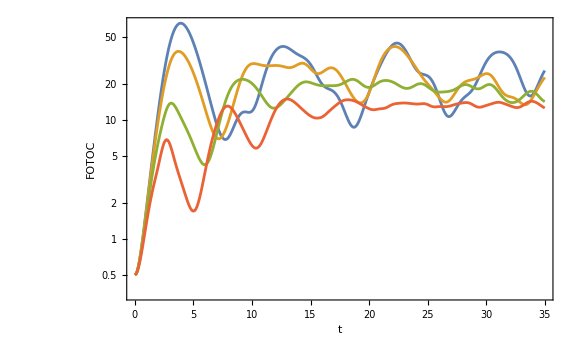

```mathematica
(*graficar FOTOCS*)
Show[ListLogPlot[Table[Transpose[{ts,ft}],{ft,ftcs}],Joined->True,Frame->True,FrameLabel->{Style["t",20],Style["FOTOC",20]},FrameTicksStyle->Large],ImageSize->Large]
```